```mathematica
f[x_, y_, x0_, y0_, b_, c_]:=b*(y-y0)+c*(Sin[x]*Sinh[y]-Sin[x0]*Sinh[y0])
inv[f_, s_]:=Function[{t},s/.FindRoot[f-t,{s, 1}]]
rootf[x_, x0_, y0_, b_, c_]:=y/.FindRoot[f[x, y, x0, y0, b, c]==0, {y, 0}]
rootf[0, Pi/2, 0.1, 1, 1]
rootf[1, Pi/2, 0.1, 1, 1]
rootf[2, Pi/2, 0.1, 1, 1]
```

0.200167

0.108602

0.104747

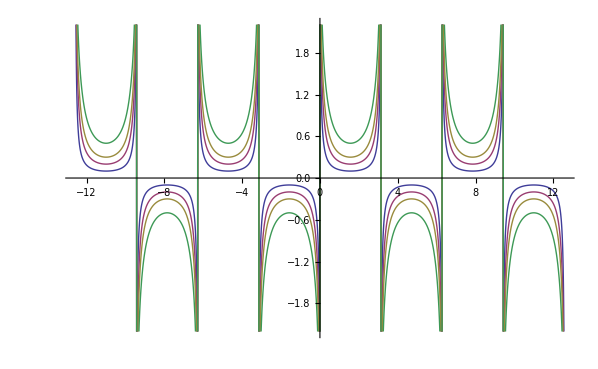

```mathematica
Plot[{rootf[x, Pi/2, 0.1, 0, 1],rootf[x, Pi/2, 0.2, 0, 1],rootf[x, Pi/2, 0.3, 0, 1],rootf[x, Pi/2, 0.5, 0, 1]}, {x, -4*Pi, 4*Pi}]
```

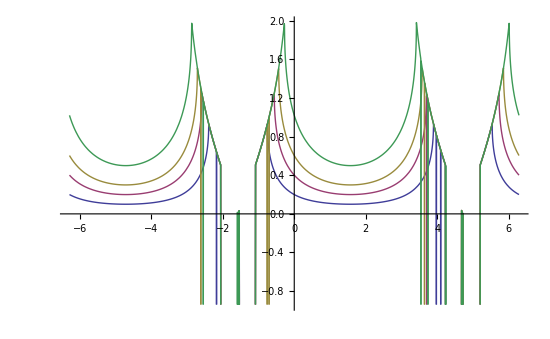

```mathematica
a=1;
b=1;
Plot[{rootf[x, Pi/2, 0.1, a, b],rootf[x, Pi/2, 0.2,a,b],rootf[x, Pi/2, 0.3, a, b],rootf[x, Pi/2, 0.5,a, b]}, {x, -2*Pi, 2*Pi}]
```

{-π/2,-π/4,0,π/4,π/2}

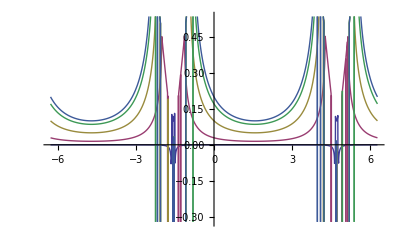

```mathematica
a=1;
b=1;
x0={-Pi/2, -Pi/4, 0, Pi/4, Pi/2}
Plot[{rootf[x, x0[[1]], 0.1, a, b],rootf[x, x0[[2]], 0.1, a, b],rootf[x, x0[[3]], 0.1, a, b],rootf[x, x0[[4]], 0.1, a, b],rootf[x, x0[[5]], 0.1, a, b]}, {x, -2*Pi, 2*Pi}]
```